## Import Levels and Create States

```mathematica
lvls = Import["/Users/ericrhudson/Documents/pghopher calculations/HCl+/Zeeman Shift/HClplus_Zero_Field_Energy.txt","CSV"]
lvls = Import["//eric.physics.ucla.edu/groups/motion/Simulation/EGGS/HClplus_Zero_Field_Energy.txt","CSV"]
```

Import::nffil: File /Users/ericrhudson/Documents/pghopher calculations/HCl+/Zeeman Shift/HClplus_Zero_Field_Energy.txt not found during Import.

$Failed

{{F,F1,parity,Eng},{0.5,0,e,0.},{0.5,0,f,77.8307},{1.5,1,e,141.739},{0.5,1,e,154.052},{1.5,1,f,223.936},{0.5,1,f,236.195},{2.5,2,e,427.781},{1.5,2,e,446.126},{2.5,2,f,514.539},{1.5,2,f,532.859},{3.5,3,e,858.829},{2.5,3,e,883.748},{3.5,3,f,941.919},{2.5,3,f,966.815}}

```mathematica
MatrixForm[
StateList = Flatten[Table[
Table[{"F"-> lvls[[ii,1]],"mF"-> jj,"F1"-> lvls[[ii,2]], "parity" -> lvls[[ii,3]], "Eng" -> lvls[[ii,4]]} , {jj,-lvls[[ii,1]],lvls[[ii,1]]}],
{ii,2,Length[lvls]}],1]
]
```

(F→0.5 | mF→-0.5 | F1→0 | parity→e | Eng→0.
F→0.5 | mF→0.5 | F1→0 | parity→e | Eng→0.
F→0.5 | mF→-0.5 | F1→0 | parity→f | Eng→77.8307
F→0.5 | mF→0.5 | F1→0 | parity→f | Eng→77.8307
F→1.5 | mF→-1.5 | F1→1 | parity→e | Eng→141.739
F→1.5 | mF→-0.5 | F1→1 | parity→e | Eng→141.739
F→1.5 | mF→0.5 | F1→1 | parity→e | Eng→141.739
F→1.5 | mF→1.5 | F1→1 | parity→e | Eng→141.739
F→0.5 | mF→-0.5 | F1→1 | parity→e | Eng→154.052
F→0.5 | mF→0.5 | F1→1 | parity→e | Eng→154.052
F→1.5 | mF→-1.5 | F1→1 | parity→f | Eng→223.936
F→1.5 | mF→-0.5 | F1→1 | parity→f | Eng→223.936
F→1.5 | mF→0.5 | F1→1 | parity→f | Eng→223.936
F→1.5 | mF→1.5 | F1→1 | parity→f | Eng→223.936
F→0.5 | mF→-0.5 | F1→1 | parity→f | Eng→236.195
F→0.5 | mF→0.5 | F1→1 | parity→f | Eng→236.195
F→2.5 | mF→-2.5 | F1→2 | parity→e | Eng→427.781
F→2.5 | mF→-1.5 | F1→2 | parity→e | Eng→427.781
F→2.5 | mF→-0.5 | F1→2 | parity→e | Eng→427.781
F→2.5 | mF→0.5 | F1→2 | parity→e | Eng→427.781
F→2.5 | mF→1.5 | F1→2 | parity→e | Eng→427.781
F→2.5 | mF→2.5 | F1→2 | parity→e | Eng→427.781
F→1.5 | mF→-1.5 | F1→2 | parity→e | Eng→446.126
F→1.5 | mF→-0.5 | F1→2 | parity→e | Eng→446.126
F→1.5 | mF→0.5 | F1→2 | parity→e | Eng→446.126
F→1.5 | mF→1.5 | F1→2 | parity→e | Eng→446.126
F→2.5 | mF→-2.5 | F1→2 | parity→f | Eng→514.539
F→2.5 | mF→-1.5 | F1→2 | parity→f | Eng→514.539
F→2.5 | mF→-0.5 | F1→2 | parity→f | Eng→514.539
F→2.5 | mF→0.5 | F1→2 | parity→f | Eng→514.539
F→2.5 | mF→1.5 | F1→2 | parity→f | Eng→514.539
F→2.5 | mF→2.5 | F1→2 | parity→f | Eng→514.539
F→1.5 | mF→-1.5 | F1→2 | parity→f | Eng→532.859
F→1.5 | mF→-0.5 | F1→2 | parity→f | Eng→532.859
F→1.5 | mF→0.5 | F1→2 | parity→f | Eng→532.859
F→1.5 | mF→1.5 | F1→2 | parity→f | Eng→532.859
F→3.5 | mF→-3.5 | F1→3 | parity→e | Eng→858.829
F→3.5 | mF→-2.5 | F1→3 | parity→e | Eng→858.829
F→3.5 | mF→-1.5 | F1→3 | parity→e | Eng→858.829
F→3.5 | mF→-0.5 | F1→3 | parity→e | Eng→858.829
F→3.5 | mF→0.5 | F1→3 | parity→e | Eng→858.829
F→3.5 | mF→1.5 | F1→3 | parity→e | Eng→858.829
F→3.5 | mF→2.5 | F1→3 | parity→e | Eng→858.829
F→3.5 | mF→3.5 | F1→3 | parity→e | Eng→858.829
F→2.5 | mF→-2.5 | F1→3 | parity→e | Eng→883.748
F→2.5 | mF→-1.5 | F1→3 | parity→e | Eng→883.748
F→2.5 | mF→-0.5 | F1→3 | parity→e | Eng→883.748
F→2.5 | mF→0.5 | F1→3 | parity→e | Eng→883.748
F→2.5 | mF→1.5 | F1→3 | parity→e | Eng→883.748
F→2.5 | mF→2.5 | F1→3 | parity→e | Eng→883.748
F→3.5 | mF→-3.5 | F1→3 | parity→f | Eng→941.919
F→3.5 | mF→-2.5 | F1→3 | parity→f | Eng→941.919
F→3.5 | mF→-1.5 | F1→3 | parity→f | Eng→941.919
F→3.5 | mF→-0.5 | F1→3 | parity→f | Eng→941.919
F→3.5 | mF→0.5 | F1→3 | parity→f | Eng→941.919
F→3.5 | mF→1.5 | F1→3 | parity→f | Eng→941.919
F→3.5 | mF→2.5 | F1→3 | parity→f | Eng→941.919
F→3.5 | mF→3.5 | F1→3 | parity→f | Eng→941.919
F→2.5 | mF→-2.5 | F1→3 | parity→f | Eng→966.815
F→2.5 | mF→-1.5 | F1→3 | parity→f | Eng→966.815
F→2.5 | mF→-0.5 | F1→3 | parity→f | Eng→966.815
F→2.5 | mF→0.5 | F1→3 | parity→f | Eng→966.815
F→2.5 | mF→1.5 | F1→3 | parity→f | Eng→966.815
F→2.5 | mF→2.5 | F1→3 | parity→f | Eng→966.815)

```mathematica
lbl = Table["StateNumber"-> ii,{ii,1,Length[StateList]}];
```

```mathematica
MatrixForm[States = Transpose[Prepend[Transpose[StateList],lbl]]]
```

(StateNumber→1 | F→0.5 | mF→-0.5 | F1→0 | parity→e | Eng→0.
StateNumber→2 | F→0.5 | mF→0.5 | F1→0 | parity→e | Eng→0.
StateNumber→3 | F→0.5 | mF→-0.5 | F1→0 | parity→f | Eng→77.8307
StateNumber→4 | F→0.5 | mF→0.5 | F1→0 | parity→f | Eng→77.8307
StateNumber→5 | F→1.5 | mF→-1.5 | F1→1 | parity→e | Eng→141.739
StateNumber→6 | F→1.5 | mF→-0.5 | F1→1 | parity→e | Eng→141.739
StateNumber→7 | F→1.5 | mF→0.5 | F1→1 | parity→e | Eng→141.739
StateNumber→8 | F→1.5 | mF→1.5 | F1→1 | parity→e | Eng→141.739
StateNumber→9 | F→0.5 | mF→-0.5 | F1→1 | parity→e | Eng→154.052
StateNumber→10 | F→0.5 | mF→0.5 | F1→1 | parity→e | Eng→154.052
StateNumber→11 | F→1.5 | mF→-1.5 | F1→1 | parity→f | Eng→223.936
StateNumber→12 | F→1.5 | mF→-0.5 | F1→1 | parity→f | Eng→223.936
StateNumber→13 | F→1.5 | mF→0.5 | F1→1 | parity→f | Eng→223.936
StateNumber→14 | F→1.5 | mF→1.5 | F1→1 | parity→f | Eng→223.936
StateNumber→15 | F→0.5 | mF→-0.5 | F1→1 | parity→f | Eng→236.195
StateNumber→16 | F→0.5 | mF→0.5 | F1→1 | parity→f | Eng→236.195
StateNumber→17 | F→2.5 | mF→-2.5 | F1→2 | parity→e | Eng→427.781
StateNumber→18 | F→2.5 | mF→-1.5 | F1→2 | parity→e | Eng→427.781
StateNumber→19 | F→2.5 | mF→-0.5 | F1→2 | parity→e | Eng→427.781
StateNumber→20 | F→2.5 | mF→0.5 | F1→2 | parity→e | Eng→427.781
StateNumber→21 | F→2.5 | mF→1.5 | F1→2 | parity→e | Eng→427.781
StateNumber→22 | F→2.5 | mF→2.5 | F1→2 | parity→e | Eng→427.781
StateNumber→23 | F→1.5 | mF→-1.5 | F1→2 | parity→e | Eng→446.126
StateNumber→24 | F→1.5 | mF→-0.5 | F1→2 | parity→e | Eng→446.126
StateNumber→25 | F→1.5 | mF→0.5 | F1→2 | parity→e | Eng→446.126
StateNumber→26 | F→1.5 | mF→1.5 | F1→2 | parity→e | Eng→446.126
StateNumber→27 | F→2.5 | mF→-2.5 | F1→2 | parity→f | Eng→514.539
StateNumber→28 | F→2.5 | mF→-1.5 | F1→2 | parity→f | Eng→514.539
StateNumber→29 | F→2.5 | mF→-0.5 | F1→2 | parity→f | Eng→514.539
StateNumber→30 | F→2.5 | mF→0.5 | F1→2 | parity→f | Eng→514.539
StateNumber→31 | F→2.5 | mF→1.5 | F1→2 | parity→f | Eng→514.539
StateNumber→32 | F→2.5 | mF→2.5 | F1→2 | parity→f | Eng→514.539
StateNumber→33 | F→1.5 | mF→-1.5 | F1→2 | parity→f | Eng→532.859
StateNumber→34 | F→1.5 | mF→-0.5 | F1→2 | parity→f | Eng→532.859
StateNumber→35 | F→1.5 | mF→0.5 | F1→2 | parity→f | Eng→532.859
StateNumber→36 | F→1.5 | mF→1.5 | F1→2 | parity→f | Eng→532.859
StateNumber→37 | F→3.5 | mF→-3.5 | F1→3 | parity→e | Eng→858.829
StateNumber→38 | F→3.5 | mF→-2.5 | F1→3 | parity→e | Eng→858.829
StateNumber→39 | F→3.5 | mF→-1.5 | F1→3 | parity→e | Eng→858.829
StateNumber→40 | F→3.5 | mF→-0.5 | F1→3 | parity→e | Eng→858.829
StateNumber→41 | F→3.5 | mF→0.5 | F1→3 | parity→e | Eng→858.829
StateNumber→42 | F→3.5 | mF→1.5 | F1→3 | parity→e | Eng→858.829
StateNumber→43 | F→3.5 | mF→2.5 | F1→3 | parity→e | Eng→858.829
StateNumber→44 | F→3.5 | mF→3.5 | F1→3 | parity→e | Eng→858.829
StateNumber→45 | F→2.5 | mF→-2.5 | F1→3 | parity→e | Eng→883.748
StateNumber→46 | F→2.5 | mF→-1.5 | F1→3 | parity→e | Eng→883.748
StateNumber→47 | F→2.5 | mF→-0.5 | F1→3 | parity→e | Eng→883.748
StateNumber→48 | F→2.5 | mF→0.5 | F1→3 | parity→e | Eng→883.748
StateNumber→49 | F→2.5 | mF→1.5 | F1→3 | parity→e | Eng→883.748
StateNumber→50 | F→2.5 | mF→2.5 | F1→3 | parity→e | Eng→883.748
StateNumber→51 | F→3.5 | mF→-3.5 | F1→3 | parity→f | Eng→941.919
StateNumber→52 | F→3.5 | mF→-2.5 | F1→3 | parity→f | Eng→941.919
StateNumber→53 | F→3.5 | mF→-1.5 | F1→3 | parity→f | Eng→941.919
StateNumber→54 | F→3.5 | mF→-0.5 | F1→3 | parity→f | Eng→941.919
StateNumber→55 | F→3.5 | mF→0.5 | F1→3 | parity→f | Eng→941.919
StateNumber→56 | F→3.5 | mF→1.5 | F1→3 | parity→f | Eng→941.919
StateNumber→57 | F→3.5 | mF→2.5 | F1→3 | parity→f | Eng→941.919
StateNumber→58 | F→3.5 | mF→3.5 | F1→3 | parity→f | Eng→941.919
StateNumber→59 | F→2.5 | mF→-2.5 | F1→3 | parity→f | Eng→966.815
StateNumber→60 | F→2.5 | mF→-1.5 | F1→3 | parity→f | Eng→966.815
StateNumber→61 | F→2.5 | mF→-0.5 | F1→3 | parity→f | Eng→966.815
StateNumber→62 | F→2.5 | mF→0.5 | F1→3 | parity→f | Eng→966.815
StateNumber→63 | F→2.5 | mF→1.5 | F1→3 | parity→f | Eng→966.815
StateNumber→64 | F→2.5 | mF→2.5 | F1→3 | parity→f | Eng→966.815)

## Define Zeeman Interaction

```mathematica
(*Here we're ignoring coupling to other rotational and electronic states*)
```

```mathematica
(*orbital bit include lambda doubling: |JΩ, *)
HL[Fp_,F_,mF_,Λ_,Ω_] := μB Λ(gL + gR) (-1)^(F-mF+Fp + J+Ispin+1+J-Ω)SixJSymbol[{J,F,Ispin},{Fp,J,1}]ThreeJSymbol[{F,-mF},{1,0},{Fp,mF}] √((2F+1)(2Fp+1)(2J+1)(2J+1))ThreeJSymbol[{J,-Ω},{1,0},{J,Ω}]
```

```mathematica
(*spin bit*)
HS[Fp_,F_,mF_,Ω_,Σ_] := μB (gS+gR) Sum[ (-1)^(F-mF+J+Ispin+Fp+1+J-Ω + S-Σ)SixJSymbol[{J,F,Ispin},{Fp,J,1}]ThreeJSymbol[{F,-mF},{1,0},{Fp,mF}] √((2F+1)(2Fp+1)(2J+1)(2J+1)S(S+1)(2S+1))ThreeJSymbol[{J,-Ω},{1,q},{J,Ω}]ThreeJSymbol[{S,-Σ},{1,q},{S,Σ}]
, {q,-1,1}]
```

```mathematica
(*Nuclear spin bit*)
(*Chlorine*)
HICl[Fp_,F_,mF_] := -gNCl μN (-1)^(F-mF+J+Ispin+Fp+1)√(Ispin(Ispin+1)(2Ispin+1)(2F+1)(2Fp+1))SixJSymbol[{Ispin,F,J},{Fp,Ispin,1}]ThreeJSymbol[{F,-mF},{1,0},{Fp,mF}]
```

```mathematica
(*Hydrogen*)
```

```mathematica
HIH[mIH_] := -gNH μN mIH
```

```mathematica
(*Rotational bit*)
HR[Fp_,F_,mF_] := gR μB (-1)^(F-mF+J+Ispin+Fp+1)√(J(J+1)(2J+1)(2F+1)(2Fp+1))SixJSymbol[{J,F,Ispin},{Fp,J,1}]ThreeJSymbol[{Fp,-mF},{1,0},{F,mF}]
```

```mathematica
(*Define functions for calculating the matrix element*)
```

```mathematica
(*matrix elements where lambda doubling matters*)
```

Basis for lambda doubling| JΩ ±⟩ = 1/(√2)(|Λ = 1; S,Σ; JΩ M_J⟩ ± (-1)^(J-S)|Λ = -1; S,-Σ; J-Ω M_J⟩)
The matrix elements are (all of these are diagonal in Λ and Ω):
⟨JΩ±| H |JΩ ±⟩ = 1/2(⟨Λ = 1; S,Σ; JΩ M_J| H |Λ = 1; S,Σ; JΩ M_J⟩ +(-1)^(2J-2S)⟨Λ = -1; S,-Σ; J-Ω M_J| H |Λ = -1; S,-Σ; J-Ω M_J⟩
2J -2S = 2*3/2 0- 2*1/2 =2
⟨JΩ±| H |JΩ ±⟩ = 1/2(⟨Λ = 1; S,Σ; JΩ M_J| H |Λ = 1; S,Σ; JΩ M_J⟩ +⟨Λ = -1; S,-Σ; J-Ω M_J| H |Λ = -1; S,-Σ; J-Ω M_J⟩

```mathematica
(*Create Hamiltonian in the lambda doubled basis*)
```

```mathematica
HLΛDouble[Fp_,F_,mF_] := 1/2(HL[Fp,F,mF,1,3/2] + HL[Fp,F,mF,-1,-3/2] )
HSΛDouble[Fp_,F_,mF_] := 1/2(HS[Fp,F,mF,3/2,1/2] + HS[Fp,F,mF,-3/2,-1/2] )
```

```mathematica
(*Works for everything except HIH*)
MatrixElement[Huse_, Fp_,mFp_,F_,mF_,F1p_,F1_] := Sum[Sum[
Conjugate[ClebschGordan[{F1p,mF1},{1/2,mIH},{Fp,mFp}]]  ClebschGordan[{F1,mF1}
,{1/2,mIH},{F,mF}]Huse[F1p,F1,mF1], {mIH,-1/2,1/2,1}],{mF1,-Min[{F1,F1p}],Min[{F1,F1p}],1}]
```

```mathematica
(*Works for HIH*)
```

```mathematica
HIHMatrixElement[ Fp_,mFp_,F_,mF_,F1p_,F1_] :=Sum[Sum[
Conjugate[ClebschGordan[{F1p,mF1},{1/2,mIH},{Fp,mFp}]]  ClebschGordan[{F1,mF1}
,{1/2,mIH},{F,mF}]HIH[mIH], {mIH,-1/2,1/2,1}],{mF1,-F1,F1,1}]
```

```mathematica
SameParityCheck[pp_,p_] := If[pp==p, 1,0]
```

```mathematica
Min[{3,2}]
```

2

## Create Zeeman Hamiltonian

```mathematica
(*Quantum Numbers*)
Ispin = 3/2;
J  = 3/2;
S = 1/2;

(*g-factors and moments*)
μB = 9.2740100657*^-24;
μN = 5.0507837393*^-27;
ℏ = 1.054571817*^-34;
(*gL,gS,gR are guesses should do the van vleck pure precession model for better estimates*)
gL = 1;
gS = 2;
gR = 5*^-4;
gNCl =0.546;
gNH = 5.5856946893;
```

```mathematica
MatrixForm[Hmag[Bz_] = 

(*add diagonals*)
Table[If[ii==jj,"Eng"/.States[[ii]],0] ,{ii,1,Length[States]},{jj,1,Length[States]}] 

+ Bz/(2π ℏ 1*^6)Table[
(*orbital*)
 MatrixElement[HLΛDouble , "F"/.States[[jj]],"mF"/.States[[jj]],"F"/.States[[ii]],"mF"/.States[[ii]],"F1"/.States[[jj]],"F1"/.States[[ii]]]SameParityCheck["parity"/.States[[jj]],"parity"/.States[[ii]]]

+

(*spin*)
MatrixElement[HSΛDouble , "F"/.States[[jj]],"mF"/.States[[jj]],"F"/.States[[ii]],"mF"/.States[[ii]],"F1"/.States[[jj]],"F1"/.States[[ii]]]SameParityCheck["parity"/.States[[jj]],"parity"/.States[[ii]]]

+

(*rotational*)
MatrixElement[HR, "F"/.States[[jj]],"mF"/.States[[jj]],"F"/.States[[ii]],"mF"/.States[[ii]],"F1"/.States[[jj]],"F1"/.States[[ii]]]SameParityCheck["parity"/.States[[jj]],"parity"/.States[[ii]]]

+

(*chlorine nuclear spin*)
MatrixElement[HICl, "F"/.States[[jj]],"mF"/.States[[jj]],"F"/.States[[ii]],"mF"/.States[[ii]],"F1"/.States[[jj]],"F1"/.States[[ii]]]SameParityCheck["parity"/.States[[jj]],"parity"/.States[[ii]]]

+

(*hydrogen nuclear spin*)
HIHMatrixElement[ "F"/.States[[jj]],"mF"/.States[[jj]],"F"/.States[[ii]],"mF"/.States[[ii]],"F1"/.States[[jj]],"F1"/.States[[ii]]]SameParityCheck["parity"/.States[[jj]],"parity"/.States[[ii]]]

,{ii,1,Length[States]}
,{jj,1,Length[States]}]];
```

SixJSymbol::tri: SixJSymbol[{3/2,0,3/2},{0,3/2,1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,0},{0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{3/2,0,3/2},{0,3/2,1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,0},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1/2,1/2},{0.5,0.5}] is not physical.

SixJSymbol::tri: SixJSymbol[{3/2,0,3/2},{0,3/2,1}] is not triangular.

General::stop: Further output of SixJSymbol::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,0},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{3/2,-3/2},{1,-1},{3/2,3/2}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

## Explore Zeeman Shift

```mathematica
(*Define a function to find the energy of a given quantum state*)
StateEngergy[Ham_, StateNumber_]:= ( 
(*Find eigenvalues and vectors*)
ES = Eigensystem[Ham];

(*create projector onto the state you want*)
proj = Table[0,{ii,1,Length[Ham]}];
proj[[StateNumber]] = 1;

(*Find the eigenvector with the maximum projection onto the desired state*)
projEvecs = Abs[ES[[2]].proj];
pos = Flatten[Position[projEvecs, Max[projEvecs]]][[1]];

Return[ {ES[[1,pos]],ES[[2,pos]]}]
)
```

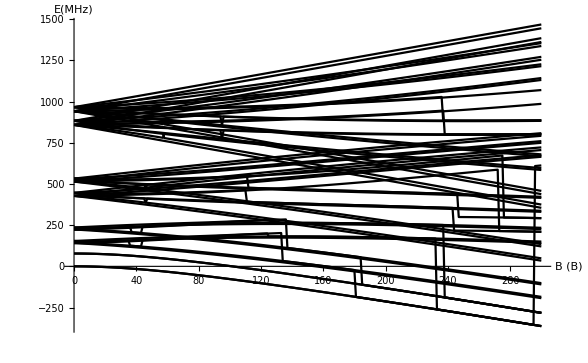

```mathematica
ListLinePlot[Table[Table[{B,StateEngergy[Hmag[B/10000.],ind][[1]]},{B,0,300,1}],{ind,1,64}],PlotStyle->Black,Background->White,AxesLabel->{"B (B)", "E(MHz)"}]
```

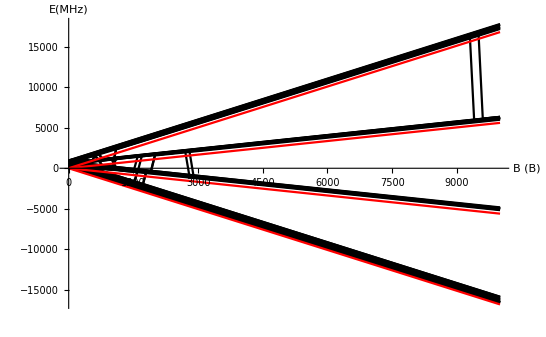

```mathematica
(*Does this make sense; at large fields it should basically just be proportional to mJ B, right?*)

Show[ListLinePlot[Table[Table[{B,StateEngergy[Hmag[B/10000.],ind][[1]]},{B,0,10000,100}],{ind,1,64}],PlotStyle->Black],Plot[{ 1/(2π ℏ 1*^6)(3/2(2μB) 3/2)/(3/2 (5/2))B/10000, 1/(2π ℏ 1*^6)(3/2(2μB) 1/2)/(3/2 (5/2))B/10000, 1/(2π ℏ 1*^6)(3/2(2μB) (-1/2))/(3/2 (5/2))B/10000, 1/(2π ℏ 1*^6)(3/2(2μB)(-3/2))/(3/2 (5/2))B/10000},{B,0,10000},PlotStyle->Red],Background->White,AxesLabel->{"B (B)", "E(MHz)"}]
```

```mathematica
(*Okay, I think this is right the Zeeman shift should be Ω μ mJ/(J(J+1) and since it's a^2 Π3/2 state I think μ is about 2μB*)
```

```mathematica
Transition[indexUpper_,indexLower_, BGauss_] := StateEngergy[Hmag[BGauss/10000.],indexUpper][[1]]-StateEngergy[Hmag[BGauss/10000.],indexLower][[1]]
```

```mathematica
States[[58]]
States[[43]]
```

{StateNumber→58,F→3.5,mF→3.5,F1→3,parity→f,Eng→941.919}

{StateNumber→43,F→3.5,mF→2.5,F1→3,parity→e,Eng→858.829}

```mathematica
States[[57]]
States[[42]]
```

{StateNumber→57,F→3.5,mF→2.5,F1→3,parity→f,Eng→941.919}

{StateNumber→42,F→3.5,mF→1.5,F1→3,parity→e,Eng→858.829}

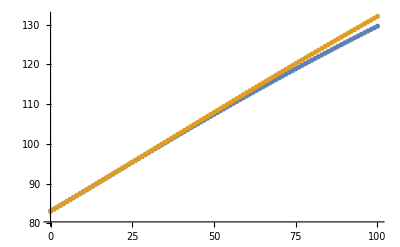

```mathematica
ListPlot[{Table[{B,Transition[58,43,B]},{B,0,100,1}],Table[{B,Transition[57,42,B]},{B,0,100,1}]}]
```

```mathematica
(*Let's look at the predictions for the various transitions*)
(*π transitions*)
States[[58]]
States[[44]]
States[[51]]
States[[37]]
```

{StateNumber→58,F→3.5,mF→3.5,F1→3,parity→f,Eng→941.919}

{StateNumber→44,F→3.5,mF→3.5,F1→3,parity→e,Eng→858.829}

{StateNumber→51,F→3.5,mF→-3.5,F1→3,parity→f,Eng→941.919}

{StateNumber→37,F→3.5,mF→-3.5,F1→3,parity→e,Eng→858.829}

```mathematica
πTransitions = Table[Transition[ 51+ii,37+ii,3.6485],{ii,0,7}]
```

{83.0905,83.0905,83.0906,83.0906,83.0906,83.0906,83.0906,83.0905}

```mathematica
σmTransitions = Table[Transition[ 51+ii,38+ii,3.6485],{ii,0,6}]
```

{81.3548,81.3492,81.3442,81.3398,81.336,81.3326,81.3296}

```mathematica
σpTransitions = Table[Transition[ 52+ii,37+ii,3.6485],{ii,0,6}]
```

{84.8263,84.832,84.837,84.8414,84.8452,84.8485,84.8514}

```mathematica
σpTransitions
```

{84.8263,84.832,84.837,84.8414,84.8452,84.8485,84.8514}

```mathematica
TransitionPlot[transitionList_] := Return[Table[{{transitionList[[ii]],0},{transitionList[[ii]],1}},{ii,1,Length[transitionList]}]]
```

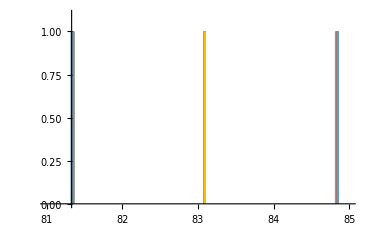

```mathematica
Show[ListLinePlot[TransitionPlot[σmTransitions]],
ListLinePlot[TransitionPlot[πTransitions]],
ListLinePlot[TransitionPlot[σpTransitions]],PlotRange-> {{81,85},{0,1.1}}]
```

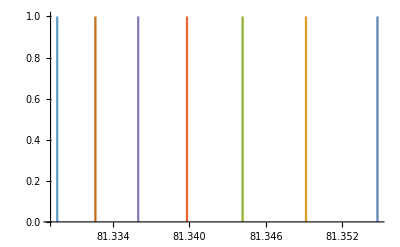

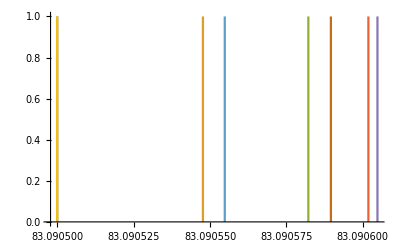

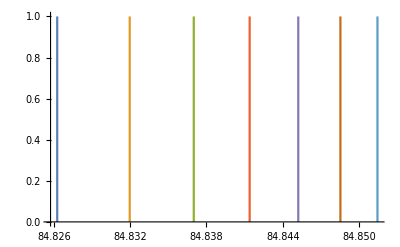

```mathematica
ListLinePlot[TransitionPlot[σmTransitions]]
ListLinePlot[TransitionPlot[πTransitions]]
ListLinePlot[TransitionPlot[σpTransitions]]
```

## Simulate spectra

```mathematica
(*Transition moment; Doesn't include parity check; leaving out reduced matrix element*)
μ[Fp_,mFp_,F1p_,F_,mF_,F1_,q_] := (-1)^(F-mF)ThreeJSymbol[{F,-mF},{1,q},{Fp,mFp}](-1)^(Fp+F1+1+1/2)√((2F+1)(2Fp+1))SixJSymbol[{F1p,Fp,1/2},{F,F1,1}](-1)^(F1p + 3/2+1 + 3/2)√((2F1+1)(2F1p+1))SixJSymbol[{3/2,F1p,3/2},{F1,3/2,1}]
```

```mathematica
States[[58]]
States[[44]]
μ[3.5,3.5,3,3.5,3.5,3,0]
```

{StateNumber→58,F→3.5,mF→3.5,F1→3,parity→f,Eng→941.919}

{StateNumber→44,F→3.5,mF→3.5,F1→3,parity→e,Eng→858.829}

0.387298

```mathematica
TransitionMoment[upperIndex_,lowerIndex_,quse_]:= Module[{jj = upperIndex, ii = lowerIndex, q = quse},
Return[μ[ "F"/.States[[jj]], "mF"/.States[[jj]],"F1"/.States[[jj]], "F"/.States[[ii]],"mF"/.States[[ii]], "F1"/.States[[ii]], q]](1-SameParityCheck["parity"/.States[[jj]],"parity"/.States[[ii]]])
]
```

```mathematica
πTransitions = Table[{Transition[ 51+ii,37+ii,3.6485], Abs[TransitionMoment[ 51+ii,37+ii,0]]^2},{ii,0,7}]
```

{{83.0905,0.15},{83.0905,0.0765306},{83.0906,0.027551},{83.0906,0.00306122},{83.0906,0.00306122},{83.0906,0.027551},{83.0906,0.0765306},{83.0905,0.15}}

```mathematica
σmTransitions = Table[{Transition[ 51+ii,38+ii,3.6485],Abs[TransitionMoment[ 51+ii,38+ii,+1]]^2},{ii,0,6}]
```

{{81.3548,0.0428571},{81.3492,0.0734694},{81.3442,0.0918367},{81.3398,0.0979592},{81.336,0.0918367},{81.3326,0.0734694},{81.3296,0.0428571}}

```mathematica
σpTransitions = Table[{Transition[ 52+ii,37+ii,3.6485],Abs[TransitionMoment[ 52+ii,37+ii,-1]]^2},{ii,0,6}]
```

{{84.8263,0.0428571},{84.832,0.0734694},{84.837,0.0918367},{84.8414,0.0979592},{84.8452,0.0918367},{84.8485,0.0734694},{84.8514,0.0428571}}

```mathematica
Spectra[f_,list_]:= Total[Table[list[[ii,1]]/(1 + 4 ((f - list[[ii,1]])/(.003))^2),{ii,1,Length[list]}]]
```

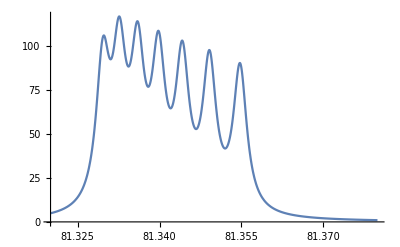

```mathematica
Plot[Spectra[f,σmTransitions], {f,81.32,81.38}]
```

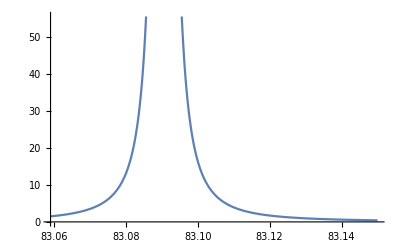

```mathematica
Plot[Spectra[f,πTransitions], {f,83.059,83.15}]
```

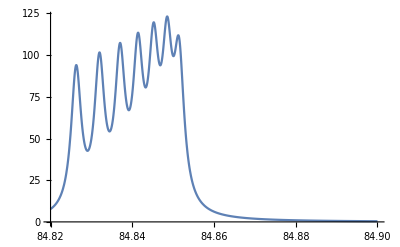

```mathematica
Plot[Spectra[f,σpTransitions], {f,84.82,84.9}]
```

```mathematica
(*Okay, the data is*)
(*-Graphics-*)
```

```mathematica
(*Is this due to F = 2, σ-?*)
(*F = 2, Ftotal = 2.5, e*)
States[[17]]
States[[22]]
```

{StateNumber→17,F→2.5,mF→-2.5,F1→2,parity→e,Eng→427.781}

{StateNumber→22,F→2.5,mF→2.5,F1→2,parity→e,Eng→427.781}

```mathematica
(*F = 2, Ftotal = 2.5, f*)
```

```mathematica
States[[27]]
States[[32]]
```

{StateNumber→27,F→2.5,mF→-2.5,F1→2,parity→f,Eng→514.539}

{StateNumber→32,F→2.5,mF→2.5,F1→2,parity→f,Eng→514.539}

```mathematica
σmTransitions2p5 = Table[{Transition[ 27+ii,18+ii,3.6485],Abs[TransitionMoment[ 27+ii,18+ii,+1]]^2},{ii,0,4}]
```

{{85.143,0.0266667},{85.1301,0.0426667},{85.1216,0.048},{85.1168,0.0426667},{85.1148,0.0266667}}

```mathematica
πTransitions2p5 = Table[{Transition[ 27+ii,17+ii,3.6485],Abs[TransitionMoment[ 27+ii,17+ii,0]]^2},{ii,0,4}]
```

{{86.7578,0.0666667},{86.7573,0.024},{86.757,0.00266667},{86.757,0.00266667},{86.7573,0.024}}

```mathematica
σpTransitions2p5 = Table[{Transition[ 28+ii,17+ii,3.6485],Abs[TransitionMoment[ 28+ii,17+ii,-1]]^2},{ii,0,4}]
```

{{88.3721,0.0266667},{88.3842,0.0426667},{88.3925,0.048},{88.3975,0.0426667},{88.4003,0.0266667}}

```mathematica
(*F = 2, Ftotal = 1.5, f*)
```

```mathematica
States[[23]]
States[[26]]
```

{StateNumber→23,F→1.5,mF→-1.5,F1→2,parity→e,Eng→446.126}

{StateNumber→26,F→1.5,mF→1.5,F1→2,parity→e,Eng→446.126}

```mathematica
(*F = 2, Ftotal = 1.5, e*)
```

```mathematica
States[[33]]
States[[36]]
```

{StateNumber→33,F→1.5,mF→-1.5,F1→2,parity→f,Eng→532.859}

{StateNumber→36,F→1.5,mF→1.5,F1→2,parity→f,Eng→532.859}

```mathematica
σmTransitions1p5 = Table[{Transition[ 33+ii,24+ii,3.6485],Abs[TransitionMoment[ 33+ii,24+ii,+1]]^2},{ii,0,2}]
```

{{84.2338,0.036},{84.28,0.048},{84.3235,0.036}}

```mathematica
πTransitions1p5 = Table[{Transition[ 33+ii,23+ii,3.6485],Abs[TransitionMoment[ 33+ii,23+ii,0]]^2},{ii,0,2}]
```

{{86.7328,0.054},{86.7323,0.006},{86.7323,0.006}}

```mathematica
σpTransitions1p5 = Table[{Transition[ 34+ii,23+ii,3.6485],Abs[TransitionMoment[ 34+ii,23+ii,-1]]^2},{ii,0,2}]
```

{{89.2314,0.036},{89.1847,0.048},{89.1417,0.036}}

```mathematica
(*So the σmTransitions 1p5 are the closest to what EGGs saw*)
```

```mathematica
(*Okay, Hao has*)
(*-Graphics-*)
```

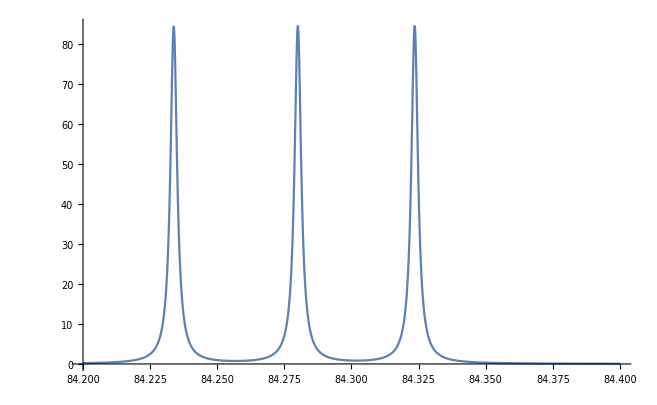

```mathematica
Plot[Spectra[f,σmTransitions1p5], {f,84.2,84.4},PlotRange->All]
```

```mathematica
(*Interesting. Would seem we only expect 3 transitions since this is the F = 1.5 part of the F1 = 2 branch... Do the splittings make sense?*)
83.467 - 83.452
83.487-83.467
```

0.015

0.02

```mathematica
σmTransitions1p5
σmTransitions1p5[[2,1]]-σmTransitions1p5[[1,1]]
σmTransitions1p5[[3,1]] - σmTransitions1p5[[2,1]]
```

{{84.2338,0.036},{84.28,0.048},{84.3235,0.036}}

0.0462255

0.0435109

```mathematica
(*Not quite... the right peak is too far away... Let's try shifting the theory and plotting over same scale*)
```

```mathematica
84.2 -83.41
```

0.79

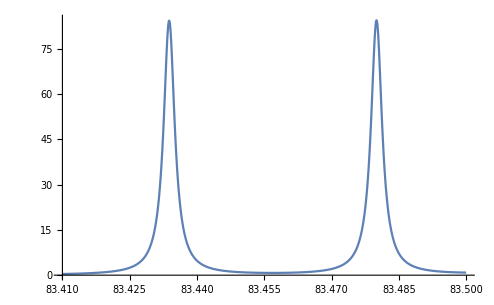

```mathematica
Plot[Spectra[f+.80,σmTransitions1p5], {f,83.41,83.5},PlotRange->All]
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*Yeah that third peak is too far to the left...*)
```

```mathematica
(*Seems reasonable I guess. need to automate this transition stuff. I just want to specify the states and have it tell me all the possible mF trnsitions*)
```

```mathematica
(*This function, defined above, gives me a transition if I give it the index of the state*)
(*Transition[indexUpper_,indexLower_, BGauss_] := StateEngergy[Hmag[BGauss/10000.],indexUpper][[1]]-StateEngergy[Hmag[BGauss/10000.],indexLower][[1]]*)
(*Now I need a function that searches my States to find all the indices with the approporiate Q#s. I just want to give it F,F1, parity of each level.*)
```

```mathematica
(*Function to find states that have the desired Q#s*)
```

```mathematica
FindIndices[F_,F1_,parity_] := ( 
surviveF1 = Position["F1"/.States, F1];
surviveF = Position["F"/.States, F];
surviveParity = Position["parity"/.States,parity];
survivors = Flatten[Intersection[surviveF,surviveF1,surviveParity]];
Return[States[[survivors,All]]]
)
```

```mathematica
FindIndices[1.5,2,"f"]
```

{{StateNumber→33,F→1.5,mF→-1.5,F1→2,parity→f,Eng→532.859},{StateNumber→34,F→1.5,mF→-0.5,F1→2,parity→f,Eng→532.859},{StateNumber→35,F→1.5,mF→0.5,F1→2,parity→f,Eng→532.859},{StateNumber→36,F→1.5,mF→1.5,F1→2,parity→f,Eng→532.859}}

```mathematica
TransitionEasy[FUpper_,F1Upper_,parityUpper_,FLower_,F1Lower_,parityLower_,B_] := (
upperStates = "StateNumber"/. FindIndices[FUpper,F1Upper,parityUpper];
lowerStates = "StateNumber"/.FindIndices[FLower,F1Lower,parityLower];
(*Print[upperStates];
Print[lowerStates];*)
σmTrans = Table[{Transition[upperStates[[1]] + ii-1,lowerStates[[1]]+ii,B],Abs[TransitionMoment[upperStates[[1]] + ii-1,lowerStates[[1]]+ii,1]]^2},{ii,1,Max[Min[Length[upperStates],Length[lowerStates]]-1,1]}];
πTrans =Table[{Transition[ upperStates[[1]] + ii,lowerStates[[1]]+ii,B],Abs[TransitionMoment[upperStates[[1]] + ii,lowerStates[[1]]+ii,0]]^2},{ii,0,Min[Length[upperStates],Length[lowerStates]]-1}];
σpTrans = Table[{Transition[ upperStates[[1]] + ii+1,lowerStates[[1]]+ii,B],Abs[TransitionMoment[upperStates[[1]] + ii+1,lowerStates[[1]]+ii,-1]]^2},{ii,0,Min[Length[upperStates],Length[lowerStates]]-2}];
Return[{Prepend[σmTrans,"σ-"],Prepend[πTrans,"π"],Prepend[σpTrans,"σ+"]}]
)
```

```mathematica
TransitionEasy[3.5,3,"e",3.5,3,"f",0]
TransitionEasy[2.5,3,"f",2.5,3,"e",0]
```

{{σ-,{-83.0905,0.0428571},{-83.0905,0.0734694},{-83.0905,0.0918367},{-83.0905,0.0979592},{-83.0905,0.0918367},{-83.0905,0.0734694},{-83.0905,0.0428571}},{π,{-83.0905,0.15},{-83.0905,0.0765306},{-83.0905,0.027551},{-83.0905,0.00306122},{-83.0905,0.00306122},{-83.0905,0.027551},{-83.0905,0.0765306},{-83.0905,0.15}},{σ+,{-83.0905,0.0428571},{-83.0905,0.0734694},{-83.0905,0.0918367},{-83.0905,0.0979592},{-83.0905,0.0918367},{-83.0905,0.0734694},{-83.0905,0.0428571}}}

{{σ-,{83.067,0.0544218},{83.067,0.0870748},{83.067,0.0979592},{83.067,0.0870748},{83.067,0.0544218}},{π,{83.067,0.136054},{83.067,0.0489796},{83.067,0.00544218},{83.067,0.00544218},{83.067,0.0489796},{83.067,0.136054}},{σ+,{83.067,0.0544218},{83.067,0.0870748},{83.067,0.0979592},{83.067,0.0870748},{83.067,0.0544218}}}

```mathematica
TransitionEasy[3.5,3,"e",3.5,3,"f",3.6485]
TransitionEasy[2.5,3,"f",2.5,3,"e",3.6485]
```

{{σ-,{-84.8263,0.0428571},{-84.832,0.0734694},{-84.837,0.0918367},{-84.8414,0.0979592},{-84.8452,0.0918367},{-84.8485,0.0734694},{-84.8514,0.0428571}},{π,{-83.0905,0.15},{-83.0905,0.0765306},{-83.0906,0.027551},{-83.0906,0.00306122},{-83.0906,0.00306122},{-83.0906,0.027551},{-83.0906,0.0765306},{-83.0905,0.15}},{σ+,{-81.3548,0.0428571},{-81.3492,0.0734694},{-81.3442,0.0918367},{-81.3398,0.0979592},{-81.336,0.0918367},{-81.3326,0.0734694},{-81.3296,0.0428571}}}

{{σ-,{80.7053,0.0544218},{80.7181,0.0870748},{80.7302,0.0979592},{80.7417,0.0870748},{80.7528,0.0544218}},{π,{83.067,0.136054},{83.0671,0.0489796},{83.0672,0.00544218},{83.0672,0.00544218},{83.0671,0.0489796},{83.067,0.136054}},{σ+,{85.4289,0.0544218},{85.4162,0.0870748},{85.4042,0.0979592},{85.3926,0.0870748},{85.3814,0.0544218}}}

```mathematica
TransitionEasy[2.5,2,"f",2.5,2,"e",3.6485]
TransitionEasy[1.5,2,"e",1.5,2,"f",3.6485]
```

{{σ-,{85.143,0.0266667},{85.1301,0.0426667},{85.1216,0.048},{85.1168,0.0426667},{85.1148,0.0266667}},{π,{86.7578,0.0666667},{86.7573,0.024},{86.757,0.00266667},{86.757,0.00266667},{86.7573,0.024},{86.7578,0.0666667}},{σ+,{88.3721,0.0266667},{88.3842,0.0426667},{88.3925,0.048},{88.3975,0.0426667},{88.4003,0.0266667}}}

{{σ-,{-89.2314,0.036},{-89.1847,0.048},{-89.1417,0.036}},{π,{-86.7328,0.054},{-86.7323,0.006},{-86.7323,0.006},{-86.7329,0.054}},{σ+,{-84.2338,0.036},{-84.28,0.048},{-84.3235,0.036}}}

```mathematica
TransitionEasy[1.5,1,"e",1.5,1,"f",3.6485]
TransitionEasy[0.5,1,"f",0.5,1,"e",3.6485]
```

{{σ-,{-83.5514,0.0111111},{-83.579,0.0148148},{-83.5292,0.0111111}},{π,{-82.1977,0.0166667},{-82.1948,0.00185185},{-82.1944,0.00185185},{-82.1977,0.0166667}},{σ+,{-80.8412,0.0111111},{-80.8103,0.0148148},{-80.863,0.0111111}}}

{{σ-,{79.44,0.0148148}},{π,{82.1423,0.00740741},{82.1427,0.00740741}},{σ+,{84.845,0.0148148}}}

```mathematica
TransitionEasy[0.5,0,"f",0.5,0,"e",3.6485]
```

SixJSymbol::tri: SixJSymbol[{0,0.5,1/2},{0.5,0,1}] is not triangular.

SixJSymbol::tri: SixJSymbol[{3/2,0,3/2},{0,3/2,1}] is not triangular.

SixJSymbol::tri: SixJSymbol[{0,0.5,1/2},{0.5,0,1}] is not triangular.

General::stop: Further output of SixJSymbol::tri will be suppressed during this calculation.

{{σ-,{77.8494,0.}},{π,{77.8349,0.},{77.8348,0.}},{σ+,{77.8203,0.}}}

```mathematica
(*Okay now that I'm looking at this, it looks like perhaps the peaks we saw could be from the σ+ transition on the F = 3/2, F1 = 1 lambda doublet:*)
```

```mathematica
TransitionEasy[1.5,1,"e",1.5,1,"f",3.6485]
```

{{σ-,{-83.5514,0.0111111},{-83.579,0.0148148},{-83.5292,0.0111111}},{π,{-82.1977,0.0166667},{-82.1948,0.00185185},{-82.1944,0.00185185},{-82.1977,0.0166667}},{σ+,{-80.8412,0.0111111},{-80.8103,0.0148148},{-80.863,0.0111111}}}

-0.07

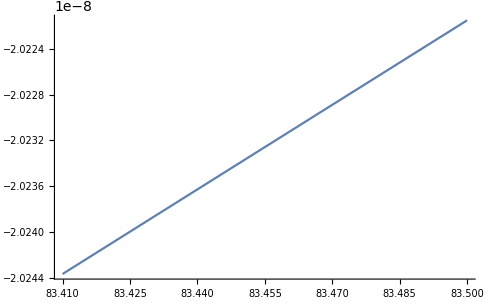

-Graphics-

```mathematica
Shift = -.07
tranUse = Drop[TransitionEasy[1.5,1,"e",1.5,1,"f",3.6485][[3]],1];
Plot[Spectra[f+Shift,tranUse], {f,83.41,83.5},PlotRange->All]
```

```mathematica
(*So it would only be one peak and perhaps this is it just hopping around do to micromotion?*)
```

```mathematica
(*To see all three peaks we'd need to blow the scale upfrom 100 kHz domain to a 300 kHz domain*)
```

0

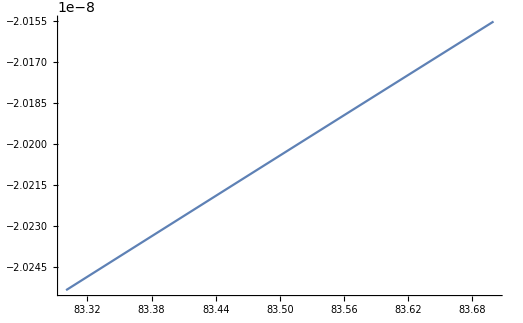

```mathematica
Shift =0
tranUse = Drop[TransitionEasy[1.5,1,"e",1.5,1,"f",3.6485][[3]],1];
Plot[Spectra[f+Shift,tranUse], {f,83.3,83.7},PlotRange->All]
```

```mathematica
(*We also see a peak at 83.31-83.34, if we assume 83.325 is the center and that it's the π transition of the "F=3"*)
```

```mathematica
TransitionEasy[3.5,3,"e",3.5,3,"f",0]
TransitionEasy[2.5,3,"f",2.5,3,"e",0]
```

{{σ-,{-83.0905,0.0428571},{-83.0905,0.0734694},{-83.0905,0.0918367},{-83.0905,0.0979592},{-83.0905,0.0918367},{-83.0905,0.0734694},{-83.0905,0.0428571}},{π,{-83.0905,0.15},{-83.0905,0.0765306},{-83.0905,0.027551},{-83.0905,0.00306122},{-83.0905,0.00306122},{-83.0905,0.027551},{-83.0905,0.0765306},{-83.0905,0.15}},{σ+,{-83.0905,0.0428571},{-83.0905,0.0734694},{-83.0905,0.0918367},{-83.0905,0.0979592},{-83.0905,0.0918367},{-83.0905,0.0734694},{-83.0905,0.0428571}}}

{{σ-,{83.067,0.0544218},{83.067,0.0870748},{83.067,0.0979592},{83.067,0.0870748},{83.067,0.0544218}},{π,{83.067,0.136054},{83.067,0.0489796},{83.067,0.00544218},{83.067,0.00544218},{83.067,0.0489796},{83.067,0.136054}},{σ+,{83.067,0.0544218},{83.067,0.0870748},{83.067,0.0979592},{83.067,0.0870748},{83.067,0.0544218}}}

```mathematica
83.31-83.067
```

0.243

```mathematica
83.34-83.0905
```

0.2495

```mathematica
(*So the other peaks we see are at:*)
```

```mathematica
(*Interesting. Would seem we only expect 3 transitions since this is the F = 1.5 part of the F1 = 2 branch... Do the splittings make sense?*)
{83.487,83.467,83.452}
```

{83.487,83.467,83.452}

```mathematica
(*Let's shift them to compare to our theory*)
{83.487,83.467,83.452}-0.24
```

{83.247,83.227,83.212}

```mathematica
(*Closest to *)
TransitionEasy[1.5,1,"e",1.5,1,"f",3.6485][[3]]
```

{σ+,{-80.8412,0.0111111},{-80.8103,0.0148148},{-80.863,0.0111111}}